#### Value function for intrinsic policy, v_int ; Variance of OU process ψ(s); Value function of OU policy, vOU; Total value function, vFull(s_c)

```mathematica
vint[ϕst_,ko_, s_, sc_]:=ϕst/ko(Exp[-ko s/ϕst]-Exp[-ko sc/ϕst])
ψ[s_,sc_,vo_,d_,ν_]:=(vo^2 d)/ν((2 ν (s-sc))/vo - Exp[-2ν(s-sc)/vo]+4Exp[-ν(s-sc)/vo]-3)+0.1
vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]:= (σ μ)/ψ[s,sc,vo,d,ν]
vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] := vint[ϕst,ko, 0, sc]+vOU[sSt,sc,vo,d,ν, σ, μ]
```

Evolution of value function of intrinsic policy

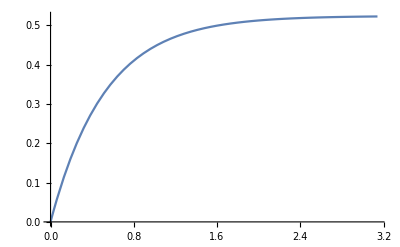

```mathematica
Plot[vint[π/6,1,0,sc],{sc,0,π},PlotRange->Automatic]
```

Evolution of variance of OU process

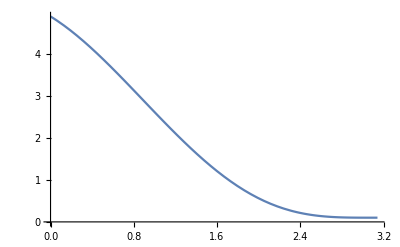

```mathematica
Plot[ψ[sc+2Cos[sc/2],sc,1,(π-sc),1],{sc,0,π},PlotRange->Automatic]
```

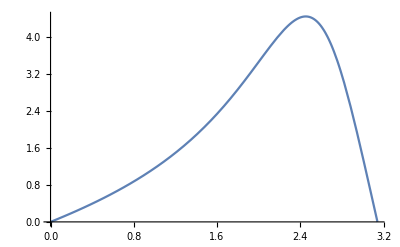

```mathematica
(*vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]*)
Plot[vOU[π,sc,1,sc^-1,1, 1,( π-sc)],{sc,0,π},PlotRange->Automatic]
```

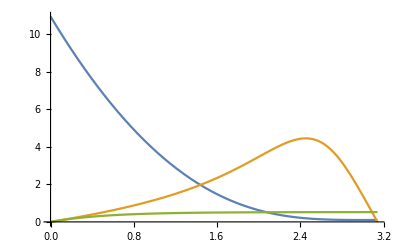

```mathematica
Plot[{ψ[π,sc,1,π-sc,1],vOU[π,sc,1,sc^-1,1, 1, π-sc],vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
```

```mathematica
vOU[sc+2Cos[sc/2],sc,1,sc^-1,1, 1,π-sc]
```

(π-sc)/(0.1+(-3-ⅇ^(-4 Cos[sc/2])+4 ⅇ^(-2 Cos[sc/2])+4 Cos[sc/2])/sc)

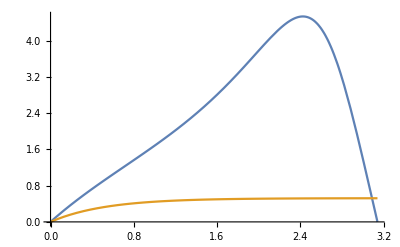

```mathematica
Plot[{vOU[sc+2Cos[sc/2],sc,1,sc^-1,1, 1,π-sc],vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
```

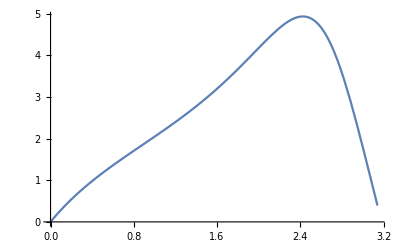

```mathematica
(*vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] *)
Plot[vFull[sc+2 Cos[sc/2], sc,1,sc^-1,1,1,π-sc,π/8,1],{sc,0,π},PlotRange->Automatic]
```

#### Non-dimensional functional forms

```mathematica
vintND[ϕst_,k_, s_, sc_]:=ϕst/k(Exp[-k s/ϕst]-Exp[-k sc/ϕst])
ψND[s_,sc_,pe_]:=pe(2  (s-sc) - Exp[-2(s-sc)]+4Exp[-(s-sc)]-3)+0.1
vOUND[s_,sc_,pe_, σ_, μ_]:= (σ μ)/ψND[s,sc,pe]
vFullND[sSt_, sc_,pe_, σ_, μ_,ϕst_,k_] := vintND[ϕst,k, 0, sc]+vOUND[sSt,sc,pe, σ, μ]
```

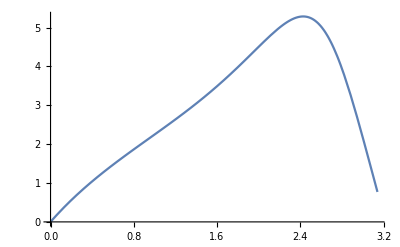

```mathematica
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,1,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]
```

```mathematica
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,1,π-sc,π/8,1],{sc,0,π},PlotRange->Automatic]
```

-Graphics-

```mathematica
voF = (5 10^-3)/10^-2
lν = voF/50
σF = 0.1/lν
```

1/2

1/100

10.

```mathematica
Integrate[Exp[-s/ϕs],{s,0,s}]
```

ϕs-ⅇ^(-s/ϕs) ϕs